# Notebook 3 : Enzyme Kinetics

The aim of this lab notebook is to familiarize users with using Mathematica ODE solvers such as DSolve and NDSolve to analyze enzyme kinetics and give them ideas of how to use advanced Mathematica-based packages such as "cellerator" to build up and analyze complex reaction networks.

1. Enzyme kinetics

### The Law of Mass Action

Biochemical kinetics is based on the mass action law, introduced by Guldberg and Wagge in the 19th century. It states that the reaction rate is proportional to the probability of a collision of the reactants. This probability is in turn proportional to the concentration of reactants to the power of the molecularity, i.e., the number in which they enter the specific reaction. For a simple reaction like 
      A  +  B (⇌_(k_-))^(k_+)  2C
  the reaction rate reads
    v = v_+-v_- = k_+ A*B - k_-C^2
 where v is the net rate , v_+ the rate of the forward reaction and v_- the rate of the backward reaction, k_+ and k_-are the so-called kinetic or rate constants. The dynamics of the concentration for this sytem is descibed by the ODEs 
 
   dA/dt=dB/dt=- v  ,    dP/dt=2 v.
 
 The genral mass action law for a reaction with substrate S_iand product concentration P_j reads:
   v = v_+-v_- = k_+ ∏_i S_i^m_i - k_-∏_j P_j^m_j,
where m_i and m_j denote the respective molecularities of S_i and P_jin this reaction.
The rate constants are related to the equlibrium constant in the following way :
K_eq = (k_+)/(k_-) =(∏_j P_j^m_j)/(∏_i S_i^m_i)

### Basic enzyme kinetics (Michaelis-Menten equation)

Consider a simple enzyme catalyzed reaction where the reaction of substrate S to form a product P is catalyzed by an enzyme E. ES is the enzyme-substrate complex in which enzyme and substrate are bound together :
     E + S (⇌_(k_-1))^(k_(+1)) ES →^(k_(+2)) E + P
With the condition that the reaction is in a steady state (i.e., ES is being made at the same rate as it is being broken down) and a couple of additional assumptions, if we denote the total concentration of enzyme as E_0, the rate of the overall reaction can be given by the well-known Michaelis-Menten equation (a nice introduction can be found at http://en.wikipedia.org/wiki/Michaelis-Menten_kinetics) :
     V = V_max S /( S+ K_M) 
where the maximum velocity V_max = k_(+2)E_0 and the Michaelis constant K_M = (k_-1 + k_(+2))/(k_(+1)). Obviously one-half of maximum velocity is achieved when substrate concentration is equal to the Michaelis constant (also named as binding constant).

In Mathematica, we can easily plot this equation (assuming K_M is 10 μM and V_max is 25 μM/second) together with its asymptote as follows:

```mathematica
V[S_,Km_,Vmax_]=Vmax (S/(Km+S));
Plot[{V[S,10,25],25},{S,0.,200},AxesLabel->{"S (μM)","V (μM/second)"},PlotStyle->{Dashing[{0.05,0}],Dashing[{0.05,0.05}]},PlotRange->All,AxesOrigin->{0,0}]
```

⁃Graphics⁃

We can also plot a series of curves for various  K_M as follows :

```mathematica
V[S_,Km_,Vmax_]=Vmax (S/(Km+S));
myplot[i_]:=Plot[V[S,i,25],{S,0.,200},AxesLabel->{"S (μM)","V (μM/second)"},PlotRange->All,AxesOrigin->{0,0}]
Show[Table[myplot[i],{i,5,20,5}]]
```

⁃Graphics⁃

### Inhibition enzyme kinetics

A number of substrates (so called as inhibitors) may cause a reduction in the rate of an enzyme catalyzed reaction. There are three kinds of inhibition : competitive inhibitors bind to the active site on the enzyme, noncompetitive inhibitors bind to a site on the enzyme distinct from the active site and uncompetitive inhibitors bind to the enzyme only when substrate is also bound to form an enzyme-substrate complex (a good tutorial can be found at http://www.lsbu.ac.uk/biology/enztech/inhibition.html). The equations for the reaction velocity for each of these three cases are :
     V_c = V_max S /( S+ (1+I/K_i)K_M) 
     V_n = V_max S /( (1+I/K_i)( S+K_M))
     V_u = V_max S /(  (1+I/K_i)S+K_M)
where V_c, V_n and  V_u denote the reaction velocity for competitive, noncompetitive and uncompetitive inhibitors, respectively. I is the concentration of inhibitor and K_i denotes the "saturation" constant for inhibitor. A nice introduction about the derivation of the equation for competitive inhibition can be found at the follwing webpage:
 http://www.bug-bytes.com/jasonf/msthesis/0A-00.html

2. Analyzing reaction networks using Cellerator™

Cellerator™ is a Mathematica® package designed to facilitate biological modeling via automated equation generation. Cellerator was designed with the intent of simulating at least the following essential biological processes: 
1.  signal transduction networks (STNs); 
2.  cells that are represented by interacting signal transduction networks; and 
3.  multi-cellular tissues that are represented by interacting networks of cells that may themselves contain internal STNs. 
Cellerator provides a framework for generating, translating, and numerically solving a potentially unlimited number of biochemical interactions. 
The website :  http://www-aig.jpl.nasa.gov/public/mls/cellerator/
For the software, please go to the download webpage : http://www.cellerator.info/download.html
For a much more detailed presentation of its usage and its power, please see demo.nb which is included in the software which you get from the download webpage.

## Prerequisite: load the packages:

```mathematica
<<xlr8r.m;
```

xlr8r 0.78 (20 Sept 2010) loaded 22 February 2012 at 16:20 GMT+00:59 using Mathematica 8.0 for Linux x86 (64-bit) (October 10, 2011) (Version 8., Release 4) (MathSBML 2.9.0 [8-Oct-2008])
GNU Lesser General Public License (LGPL) Terms Apply.

## Illustrate Cellerator Help

```mathematica
?help
```

Global`help

```mathematica
help[mergeIndices]
```

help[mergeIndices]

```mathematica
?Cellerator
```

Information::notfound: Symbol "Cellerator" not found.

```mathematica
?arrows
```

Arrows. Cellerator uses the following arrows: 
→	or \[ShortRightArrow]
↦	or \[RightTeeArrow]
⇄	or \[RightArrowLeftArrow]
⟹	or \[DoubleLongRightArrow] or Esc==>Esc
⇌ or \[Equilibrium] or EscequiEsc (note: Equilibrium is just the name used by Mathematica; this arrow does NOT denote Equilibrium!)
In addition, over- and underscripts are used to indicate catalytic (enzymatic) reactions. The under/overscripts are over/under the entire reaction, not just the arrow. Arrows should be entered using the Cellerator Palette to ensure the correct syntax.See also arrow. 
The arrow used for reactions (→) is not the same symbol as the arrow used for option lists (→). The arrow used for option lists can be entered using the keyboard -> character combination. 
The following classes of cellerator arrows are defined:
S→P Conversion of S to P
S→∅ Annihilation of S
∅→P Creation of P
S⇄P Reversible conversion between S and P. Biochemical equivalent: {S→P, P→S}
S ⇄ P X Catalytic reaction, coversion of S to P is faciliated by X with the formation of an intermediate compound. Biochemical equivalent: S+X⇄SX→X+P
S ⇌ P X Catalytic reaction with two intermediate complexes. Biochemical equivalent is S+X⇄SX⇄PX⇄X+P
S ⇄ P Y X Reversible catalytic reaction, the conversion of S to P is facilated by X and the conversion of P to S is facilitated by Y. Typically X is a kinase and Y is a phosphatase. Biochemical equivalent:{S+X⇄SX→X+P, P+Y⇄PY→S+Y}
S → P x Catalytic reaction without formation of intermediate compout. Biochemical equivalent: S+X→P+X
S ↦ P X the conversion of S to P is saturable in S and proceeds at a rate that is proportional to X as dP/dt=S^n (r + v X)/K^n + S^n where n, r, v, and K are constants.
S↦P Production of P occurs at a rate that depends upon S according to one of the Right-Tee-Arrow functions:hill, GRN, NHCA, SSystem.
{S⟹P, MM[KD,V} Michaelis-Menten with dP/dt=V*S/KD + S
{S⟹P enz, MM[KD,V} Michaelis-Menten with dP/dt=V*S*enz/KD + S
{S⟹P enz, MM[k1,k2,k3} Michaelis-Menten with dP/dt=k3*S*enz/k2 + k3/k1 + S
{S↦P,hill[...]}  dP/dt=k+r + v S^n/K^n + S^n, where k, K, r, v, n are constants;
{S↦P,GRN[...]}  dP/dt=r/1 + ⅇ^-h - T S^n, where h,T, n, r are constants(GRN);
{S↦P,NHCA[...]}  dP/dt=(1 + T S^n)^m/k (1 + R S^n)^m + (1 + T S^n)^m, where R, T, k, n, m are constants.(NHCA, non-heirarchical cooperative activation))
{S↦P,SSystem[...]}  dP/dt= 1/τ(k^+∏ iS_i c_i +-k^- ∏ iS_i c_i -) (SSystem)
{S1, S2,  ... }⟹{P1, P2,  ... } {{A1, A2,  ... }, {I1, I2,  ... }} Enzyme dP/dt=Enzyme*kcatGMWC*((Π Si/KSi)(Π(1+Si/KSi)^n - 1 )(Π(1+Ai/KAi)^n)+L*(Π c*Si/KSi)(Π(1 + c*Si/KSi)^n - 1 )(Π(1 + Ii/KIi)^n))/((Π(1 + Si/KSi)^n )(Π(1+Ai/KAi)^n)+L *(Π(1 + c*Si/KSi)^n )(Π(1 + Ii/KIi)^n)) where c, L, v, n are constants (GMWC, Generalized MWC).
{S1, S2,  ... }⟹{P1, P2,  ... } {{A1, A2,  ... }, {I1, I2,  ... },  {{JS11, JS12,  ... }, {JS21, JS22,  ... },   ... , {JA11, JA12,  ... }, {JA21,  ... },  ... }} Enzyme dP/dt=Enzyme*kcatGMWC*((Π Si/KSi)(Π(1+Si/KSi+Σ_pJS_ip/KJS_ip)^n - 1 )(Π(1+Ai/KAi+Σ_jJ_ij/KJ_ij)^n)+L*(Π c*Si/KSi)(Π(1+c*Si/KSi+Σ_pJS_ip/KJS_ip)^n - 1 )(Π(1 + Ii/KIi)^n))/((Π(1+Si/KSi+Σ_pJS_ip/KJS_ip)^n )(Π(1+Ai/KAi+Σ_jJ_ij/KJ_ij)^n)+L *(Π(1+c*Si/KSi+Σ_pJS_ip/KJS_ip)^n )(Π(1 + Ii/KIi)^n))(GMWC with competitive inhibition)
See also arrow[...] for text equivalents to all arrows.

## Different Types of Enzymatic Arrows

#### Demonstrate the arrow (S⇌P)^enz

```mathematica
lowLevelReactions[{{Overscript[S⇌P, enz]}}]
```

Missing rate constants in the reaction {(S⇌P)^enz} set to a value of 1

{{enz+S→Bind[enz,S],1},{Bind[enz,S]→enz+S,1},{Bind[enz,S]→Bind[enz,P],1},{Bind[enz,P]→Bind[enz,S],1},{Bind[enz,P]→enz+P,1},{enz+P→Bind[enz,P],1}}

```mathematica
lowLevelReactions[{{Overscript[S⇄P, enz]}}]
```

{{enz+S→Bind[enz,S],1},{Bind[enz,S]→enz+S,1},{Bind[enz,S]→enz+P,1}}

```mathematica
interpret[{{Overscript[S⇌P, e], k1,k2,k3,k4,k5,k6}}][[1]]//TableForm
```

e'[t]==-k6 e[t] P[t]-k1 e[t] S[t]+k5 Bind[e,P][t]+k2 Bind[e,S][t]
P'[t]==-k6 e[t] P[t]+k5 Bind[e,P][t]
S'[t]==-k1 e[t] S[t]+k2 Bind[e,S][t]
Bind[e,P]'[t]==k6 e[t] P[t]-k4 Bind[e,P][t]-k5 Bind[e,P][t]+k3 Bind[e,S][t]
Bind[e,S]'[t]==k1 e[t] S[t]+k4 Bind[e,P][t]-k2 Bind[e,S][t]-k3 Bind[e,S][t]

```mathematica
interpret[{{Overscript[S⇄P, e], k1,k2,k3,k4,k5,k6}}][[1]]//TableForm
```

Warning: the extra rate constants {k5,k6} will be ignored in the reaction {(S⇄P)^e,k1,k2,k3,k4,k5,k6}

e'[t]==-k4 e[t] P[t]-k1 e[t] S[t]+k2 Bind[e,S][t]+k3 Bind[e,S][t]
P'[t]==-k4 e[t] P[t]+k3 Bind[e,S][t]
S'[t]==-k1 e[t] S[t]+k2 Bind[e,S][t]
Bind[e,S]'[t]==k4 e[t] P[t]+k1 e[t] S[t]-k2 Bind[e,S][t]-k3 Bind[e,S][t]

#### If fewer than six constants are supplied they are zero-filled

```mathematica
interpret[{{Overscript[S⇌P, e], k1,k2,k3,k4}}][[1]]//TableForm
```

Missing rate constants in the reaction {(S⇌P)^e,k1,k2,k3,k4} set to a value of 1

e'[t]==-e[t] P[t]-k1 e[t] S[t]+Bind[e,P][t]+k2 Bind[e,S][t]
P'[t]==-e[t] P[t]+Bind[e,P][t]
S'[t]==-k1 e[t] S[t]+k2 Bind[e,S][t]
Bind[e,P]'[t]==e[t] P[t]-Bind[e,P][t]-k4 Bind[e,P][t]+k3 Bind[e,S][t]
Bind[e,S]'[t]==k1 e[t] S[t]+k4 Bind[e,P][t]-k2 Bind[e,S][t]-k3 Bind[e,S][t]

```mathematica
interpret[{{Overscript[S⇄P, e], k1,k2,k3,k4}}][[1]]//TableForm
```

e'[t]==-k4 e[t] P[t]-k1 e[t] S[t]+k2 Bind[e,S][t]+k3 Bind[e,S][t]
P'[t]==-k4 e[t] P[t]+k3 Bind[e,S][t]
S'[t]==-k1 e[t] S[t]+k2 Bind[e,S][t]
Bind[e,S]'[t]==k4 e[t] P[t]+k1 e[t] S[t]-k2 Bind[e,S][t]-k3 Bind[e,S][t]

## Example 1 - Building up a simple reaction network; "interpret" and "run" commands

```mathematica
myreactions={
{Overscript[A⇄B, C],1,.01,1,1.5,.02,1.7}, 
{A⇄∅,.25,.25},{C↦A,hill[vmax-> 1.5,nhill-> 3,khalf-> 2.7]}
}
```

{{(A⇄B)^C,1,0.01,1,1.5,0.02,1.7},{A⇄∅,0.25,0.25},{C↦A,hill[1.5,2.7,3,0,1]}}

```mathematica
lowLevelReactions[myreactions]
```

Warning: the extra rate constants {0.02,1.7} will be ignored in the reaction {(A⇄B)^C,1,0.01,1,1.5,0.02,1.7}

{{A+C→Bind[A,C],1},{Bind[A,C]→A+C,0.01},{Bind[A,C]→B+C,1},{B+C→Bind[A,C],1.5},{A→∅,0.25},{∅→A,0.25},{C↦A,hill[1.5,2.7,3,0,1]}}

```mathematica
interpret[myreactions]
```

Warning: the extra rate constants {0.02,1.7} will be ignored in the reaction {(A⇄B)^C,1,0.01,1,1.5,0.02,1.7}

{{A'[t]==0.25-0.25 A[t]-A[t] C[t]+(3.375 C[t]^3)/(19.683+3.375 C[t]^3)+0.01 Bind[A,C][t],B'[t]==-1.5 B[t] C[t]+Bind[A,C][t],C'[t]==-A[t] C[t]-1.5 B[t] C[t]+1.01 Bind[A,C][t],Bind[A,C]'[t]==A[t] C[t]+1.5 B[t] C[t]-1.01 Bind[A,C][t]},{A,B,C,Bind[A,C]}}

```mathematica
lowLevelReactions[myreactions]
```

Warning: the extra rate constants {0.02,1.7} will be ignored in the reaction {(A⇄B)^C,1,0.01,1,1.5,0.02,1.7}

{{A+C→Bind[A,C],1},{Bind[A,C]→A+C,0.01},{Bind[A,C]→B+C,1},{B+C→Bind[A,C],1.5},{A→∅,0.25},{∅→A,0.25},{C↦A,hill[1.5,2.7,3,0,1]}}

Warning: the extra rate constants {0.02,1.7} will be ignored in the reaction {(A⇄B)^C,1,0.01,1,1.5,0.02,1.7}

ToExpression::notstrbox: SuperscriptBox[
 is not a string or a box. ToExpression can only interpret strings or boxes as Mathematica input.

ToExpression::notstrbox: SuperscriptBox[ is not a string or a box. ToExpression can only interpret strings or boxes as Mathematica input.

General::stop: Further output of ToExpression :: notstrbox will be suppressed during this calculation.

Complement::heads: Heads List and MathSBML`Private`Xpression2SymbolicMathML at positions 2 and 1 are expected to be the same.

Complement::heads: Heads List and Complement at positions 2 and 1 are expected to be the same.

Context::ssle: Symbol, string, or HoldPattern[symbol] expected at position 1 in Context[Complement[MathSBML`Private`Xpression2SymbolicMathML[{$Failed, $Failed, $Failed, $Failed, $Failed, $Failed, $Failed, $Failed}], {If}]].

Context::ssle: Symbol, string, or HoldPattern[symbol] expected at position 1 in Context[{A, B, C, Bind[A, C]}].

Context::ssle: Symbol, string, or HoldPattern[symbol] expected at position 1 in Context[{A, B, Bind, C}].

General::stop: Further output of Context :: ssle will be suppressed during this calculation.

Complement::argm: Complement called with 0 arguments; 1 or more arguments are expected.

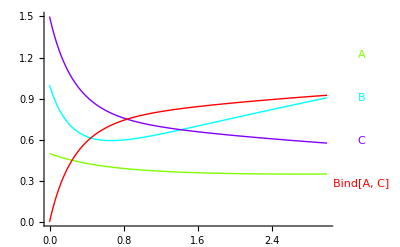

{{A→InterpolatingFunction[{{0.,3.}},<>],B→InterpolatingFunction[{{0.,3.}},<>],C→InterpolatingFunction[{{0.,3.}},<>],Bind[A,C]→InterpolatingFunction[{{0.,3.}},<>]}}

```mathematica
r=run[myreactions,initialConditions-> {A[0]==0.5,B[0]==1.0, C[0]==1.5},
timeSpan-> {0,3},
plot->True]
```

## Example 2 - Building the same network with Text-based commands

```mathematica
run[{
arrow["Catalytic",A,B,C,.01,1,1.5,.02,1.7],
arrow["Reversible",A,Vacuum,.25,.25],
arrow["HillFunction",C,A,vmax-> 1.5,nhill-> 3,khalf-> 2.7]
},
timeSpan-> 15, 
initialConditions-> {A[0]==0.5,B[0]==1.0, C[0]==1.5},
plotVariables-> All,plotColumns-> 2,
showODEs-> True
]
```

Not a list of lists.

Part::partw: Part 2 of {} does not exist.

Complement::heads: Heads List and Part at positions 2 and 1 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Join::heads: Heads Part and List at positions 1 and 2 are expected to be the same.

ToExpression::notstrbox: Join[{} ⟦ 1 ⟧, {A[0] == 0.5, B[0] == 1., C[0] == 1.5}, True] is not a string or a box. ToExpression can only interpret strings or boxes as Mathematica input.

Complement::heads: Heads List and MathSBML`Private`Xpression2SymbolicMathML at positions 2 and 1 are expected to be the same.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partd: Part specification List ⟦ 2 ⟧ is longer than depth of object.

Complement::heads: Heads Part and Complement at positions 2 and 1 are expected to be the same.

General::stop: Further output of Complement :: heads will be suppressed during this calculation.

Context::ssle: Symbol, string, or HoldPattern[symbol] expected at position 1 in Context[Complement[MathSBML`Private`Xpression2SymbolicMathML[$Failed], {If}]].

Context::ssle: Symbol, string, or HoldPattern[symbol] expected at position 1 in Context[{} ⟦ 2 ⟧].

Context::ssle: Symbol, string, or HoldPattern[symbol] expected at position 1 in Context[2 ⟦ List ⟧].

General::stop: Further output of Context :: ssle will be suppressed during this calculation.

Complement::argm: Complement called with 0 arguments; 1 or more arguments are expected.

Join::heads: Heads Part and List at positions 1 and 2 are expected to be the same.

NDSolve::deqn: Equation or list of equations expected instead of Join[{} ⟦ 1 ⟧, {A[0] == 0.5, B[0] == 1., C[0] == 1.5}, True] in the first argument Join[{} ⟦ 1 ⟧, {A[0] == 0.5, B[0] == 1., C[0] == 1.5}, True].

NDSolve[Join[{}⟦1⟧,{A[0]==0.5,B[0]==1.,C[0]==1.5},True],{}⟦2⟧,{t,0,15}]

3. Exercises

### Exercise 1 : Ionic channel kinetics

An ionic channel (ion channels can be regarded as special enzymes for mediating ion transportation) can exist in three states : S_1,S_2,S_3. S_1 and S_3 represent closed states (no ions can pass through the channel) and S_2 is an open state. On a given cell there are a number of channels and the fractions of channels in states S_1,S_2 and S_3 are designated x, y and z respectively. Transitions between the states follow the schematic diagram :          S_1(⇌_k_3)^k_1 S_2→^k_2 S_3 ,
where k_1,k_2 and k_3 are positive rate constants. A differential equation for this system is : 
dx/dt=- k_1 x+k_3 y, dy/dt=k_1 x-(k_2+k_3) y, dz/dt=k_2 y
where 1≥x≥0, 1≥y≥0 , 1≥z≥0 and let us assume k_1=2, k_2=2 and k_3=1
(i.) Sketch the flow in the x,y plane ( Hint: using PlotVectorField and flow in the (x,y) plane means the direction field (dx/dt,dy/dt)) and the flow in the y,z plane.
(ii.) Using NDSolve to solve the equations and give graphs showing x, y ,z as a function of time starting from initial conditions of (a) x = 1, y = 0, z = 0; (b)  x = 0, y = 1, z = 0.  Give an intuitive explanation of why z  eventually goes to 1  in both cases. 
(iii.) Assume an initial condition of x = 0, y = 1, z = 0 and assume k_1=0, k_2=2 and k_3=1, solve for x, y, z as a function of time and give an intuitive explanation of why z does not increase to 1 in this case; Now assume k_1=0 and k_2,k_3 are arbitary positive numbers, calculate the final proportions of x and z in terms of k_2 and k_3 (Hint: Using DSolve here).
(iv.) (optional) Find a single second - order linear ordinary differential equation for y in which all terms containing x and z have been eliminated and  solve this equation starting with an initial condition of x = 0, y = 1 and z = 0.

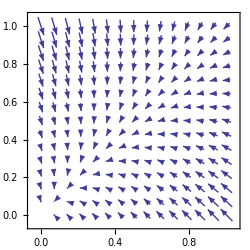

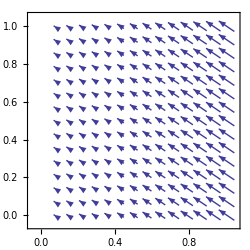

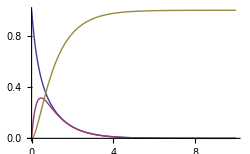

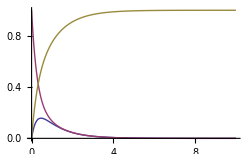

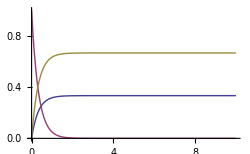

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot :: rect will be suppressed during this calculation.

MapThread::mptd: Object {{0, 1, k3/k2}, {0, 0, -k2 - k3/k2}, {1, 0, 1}} . {{{}, 0, 0}, {0, {}, 0}, {0, 0, {}}} . {k2\ C[2]/k2 + k3 + C[3], C[1] + k3\ C[2]/k2 + k3, -k2\ C[2]/k2 + k3} at position {2, 2} in MapThread[Rule, {{x[t], y[t], z[t]}, {{0, 1, k3/k2}, {0, 0, Times[« 2 »] + Times[« 2 »]/k2}, {1, 0, 1}} . {{{}, 0, 0}, {0, {}, 0}, {0, 0, {}}} . {k2\ C[2]/Plus[« 2 »] + C[3], C[1] + k3\ C[2]/Plus[« 2 »], -k2\ C[2]/k2 + k3}}] has only 0 of required 1 dimensions.

ReplaceAll::reps: {MapThread[Rule, {{x[t], y[t], z[t]}, {{0, 1, Power[« 2 »]\ k3}, {0, 0, Power[« 2 »]\ Plus[« 2 »]}, {1, 0, 1}} . {{{}, 0, 0}, {0, {}, 0}, {0, 0, {}}} . {k2\ Power[« 2 »]\ C[« 1 »] + C[3], C[1] + k3\ Power[« 2 »]\ C[« 1 »], -k2\ C[2]/Plus[« 2 »]}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {MapThread[Rule, {{x[t], y[t], z[t]}, {{0, 1, Times[« 2 »]}, {0, 0, Times[« 2 »]}, {1, 0, 1}} . {{{}, 0, 0}, {0, {}, 0}, {0, 0, {}}} . {Times[« 3 »] + C[« 1 »], C[« 1 »] + Times[« 3 »], -k2\ Power[« 2 »]\ C[« 1 »]}}] == 0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

MapThread::mptd: Object {{0, 1, k3/k2}, {0, 0, -k2 - k3/k2}, {1, 0, 1}} . {{{}, 0, 0}, {0, {}, 0}, {0, 0, {}}} . {Reduce`ReduceVar[1] + k2\ Reduce`ReduceVar[2]/k2 + k3, k3\ Reduce`ReduceVar[2]/k2 + k3 + Reduce`ReduceVar[3], -k2\ Reduce`ReduceVar[2]/k2 + k3} at position {2, 2} in MapThread[Rule, {{x[t], y[t], z[t]}, {{0, 1, k3/k2}, {0, 0, Times[« 2 »] + Times[« 2 »]/k2}, {1, 0, 1}} . {{{}, 0, 0}, {0, {}, 0}, {0, 0, {}}} . {Reduce`ReduceVar[1] + k2\ Reduce`ReduceVar[2]/Plus[« 2 »], k3\ Reduce`ReduceVar[2]/Plus[« 2 »] + Reduce`ReduceVar[3], -k2\ Reduce`ReduceVar[2]/k2 + k3}}] has only 0 of required 1 dimensions.

ReplaceAll::reps: {MapThread[Rule, {{x[t], y[t], z[t]}, {{0, 1, Times[« 2 »]}, {0, 0, Times[« 2 »]}, {1, 0, 1}} . {{{}, 0, 0}, {0, {}, 0}, {0, 0, {}}} . {Reduce`ReduceVar[« 1 »] + Times[« 3 »], Times[« 3 »] + Reduce`ReduceVar[« 1 »], -k2\ Power[« 2 »]\ Reduce`ReduceVar[« 1 »]}}] == 0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Solve::naqs: {z[0], x[0], -1 + y[0]} == 0/. MapThread[Rule, {{x[t], y[t], z[t]}, {{0, 1, Times[« 2 »]}, {0, 0, Times[« 2 »]}, {1, 0, 1}} . {{{}, 0, 0}, {0, {}, 0}, {0, 0, {}}} . {Times[« 3 »] + C[« 1 »], C[« 1 »] + Times[« 3 »], -k2\ Power[« 2 »]\ C[« 1 »]}}] == 0
 is not a quantified system of equations and inequalities.

MapThread::mptd: Object {{0, 1, k3/k2}, {0, 0, -k2 - k3/k2}, {1, 0, 1}} . {{{}, 0, 0}, {0, {}, 0}, {0, 0, {}}} . {Reduce`ReduceVar[1] + k2\ Reduce`ReduceVar[2]/k2 + k3, k3\ Reduce`ReduceVar[2]/k2 + k3 + Reduce`ReduceVar[3], -k2\ Reduce`ReduceVar[2]/k2 + k3} at position {2, 2} in MapThread[Rule, {{x[t], y[t], z[t]}, {{0, 1, k3/k2}, {0, 0, Times[« 2 »] + Times[« 2 »]/k2}, {1, 0, 1}} . {{{}, 0, 0}, {0, {}, 0}, {0, 0, {}}} . {Reduce`ReduceVar[1] + k2\ Reduce`ReduceVar[2]/Plus[« 2 »], k3\ Reduce`ReduceVar[2]/Plus[« 2 »] + Reduce`ReduceVar[3], -k2\ Reduce`ReduceVar[2]/k2 + k3}}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread :: mptd will be suppressed during this calculation.

Solve::naqs: {z[0], x[0], -1 + y[0]} == 0/. MapThread[Rule, {{x[t], y[t], z[t]}, {{0, 1, Times[« 2 »]}, {0, 0, Times[« 2 »]}, {1, 0, 1}} . {{{}, 0, 0}, {0, {}, 0}, {0, 0, {}}} . {Times[« 3 »] + C[« 1 »], C[« 1 »] + Times[« 3 »], -k2\ Power[« 2 »]\ C[« 1 »]}}] == 0
 is not a quantified system of equations and inequalities.

DSolve::bvfail: For some branches of the general solution, unable to solve the conditions.

{}

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{}

```mathematica
VectorPlot[{-2x+y,2x-3y},{x,0,1},{y,0,1},ImageSize->250]
VectorPlot[{2 0-3y,2y},{y,0,1},{z,0,1},ImageSize->250]

sol1=NDSolve[{x'[t]== -2x[t]+ y[t],y'[t]==2x[t]-3y[t],z'[t]==2y[t],z[0]==0,x[0]==1,y[0]==0},{x,y,z},{t,0,10}];
Plot[{Evaluate[x[t]/.sol1],Evaluate[y[t]/.sol1],Evaluate[z[t]/.sol1]},{t,0,10},PlotRange->All,ImageSize->250]
sol2=NDSolve[{x'[t]== -2x[t]+ y[t],y'[t]==2x[t]-3y[t],z'[t]==2y[t],z[0]==0,x[0]==0,y[0]==1},{x,y,z},{t,0,10}];
Plot[{Evaluate[x[t]/.sol2],Evaluate[y[t]/.sol2],Evaluate[z[t]/.sol2]},{t,0,10},PlotRange->All,ImageSize->250]

sol3=NDSolve[{x'[t]== -0x[t]+ y[t],y'[t]==0x[t]-3y[t],z'[t]==2y[t],z[0]==0,x[0]==0,y[0]==1},{x,y,z},{t,0,10}];
Plot[{Evaluate[x[t]/.sol3],Evaluate[y[t]/.sol3],Evaluate[z[t]/.sol3]},{t,0,10},PlotRange->All,ImageSize->250]

sol4=DSolve[{x'[t]== -0x[t]+ k3 y[t],y'[t]==0x[t]-(k2 + k3)y[t],z'[t]==k2 y[t],z[0]==0,x[0]==0,y[0]==1},{x,y,z},t]

sol5=DSolve[{y''[t] == (k2 + k3)^2y[t],y[0]==1,y'[0]==-(k2+k3),y''[0]==(k2+k3)^2},{y},t]
```

### Exercise 2: Enzyme inhibition kinetics

Plot the reaction velocity V as a function of substrate concentration S  for a Michaelis-Menten enzyme catalyzed reaction with various concentrations of a competitive, non-competitive, and uncompetitive inhibitor. Use V_max = 1.0 mM/second, K_M=1.0mM, K_i=1.0mM and  I=0,2,5,10mM.  What happens when the inhibitor concentration increases? What are the differences between competitive, non-competitive, and uncompetitive inhibitions? (Please note that a good tutorial can be found at http://www.lsbu.ac.uk/biology/enztech/inhibition.html)

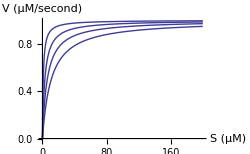

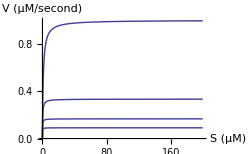

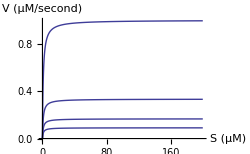

```mathematica
Vc[S_,Km_,Ki_,Vmax_,R_]=Vmax S/(S+(1+R/Ki) Km);
Vu[S_,Km_,Ki_,Vmax_,R_]=Vmax S/((1+R/Ki)S+Km);
Vn[S_,Km_,Ki_,Vmax_,R_]=Vmax S/((1+R/Ki)(S+Km));
myplot[A_,i_]:=Plot[A[S,1.0,1.0,1.0,i],{S,0.,200},AxesLabel->{"S (μM)","V (μM/second)"},PlotRange->All,AxesOrigin->{0,0}]
Show[Table[myplot[Vc,i],{i,{0,2,5,10}}],ImageSize->250]
Show[Table[myplot[Vu,i],{i,{0,2,5,10}}],ImageSize->250]
Show[Table[myplot[Vn,i],{i,{0,2,5,10}}],ImageSize->250]
```

### Exercise 3: Lineweaver-Burke Plot

Lineweaver-Burke is the plot of 1/V against 1/S.  (i) Please generate the corresponding  Lineweaver-Burke Plots for the example shown in Section 1  (i.e., enzyme catalyzed reaction with K_M is 10 μM and V_max is 25 μM/second and S = 5,10,15,20μM) . 
(ii) Please generate the corresponding  Lineweaver-Burke Plots for the inhibition kinetics in Exercise 2.  Explain what are the advantages of  Lineweaver-Burke plot over the normal Michaelis-Menten plot.

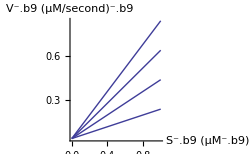

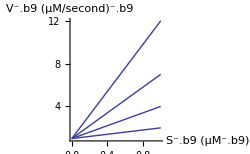

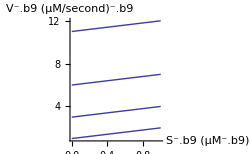

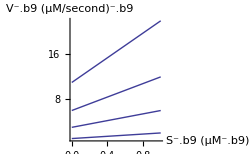

```mathematica
V[S_,Km_,Vmax_]=Vmax (S/(Km+S));
myplot[i_]:=Plot[1/V[1/Sinv,i,25],{Sinv,0,1},AxesLabel->{"S⁻.b9 (μM⁻.b9)","V⁻.b9 (μM/second)⁻.b9"},PlotRange->All,AxesOrigin->{0,0}]
Show[Table[myplot[i],{i,5,20,5}],ImageSize->250]

myplot[A_,i_]:=Plot[1/A[1/Sinv,1.0,1.0,1.0,i],{Sinv,0.,1},AxesLabel->{"S⁻.b9 (μM⁻.b9)","V⁻.b9 (μM/second)⁻.b9"},PlotRange->All,AxesOrigin->{0,0}]
Show[Table[myplot[Vc,i],{i,{0,2,5,10}}],ImageSize->250]
Show[Table[myplot[Vu,i],{i,{0,2,5,10}}],ImageSize->250]
Show[Table[myplot[Vn,i],{i,{0,2,5,10}}],ImageSize->250]
```

### Exercise 4: Derivation of rate equations (optional)

Read the following webpage carefully : http://www.bug-bytes.com/jasonf/msthesis/0A-00.html . Please use your own words to describe how you can derive the rate equations for competitive inhibition kinetics and Michaelis-Menten kinetics.

### Exercise 5: A Simple Model of Voltage - Dependent Gating Channel

Channels can be thought to have gates that regulate the permeability of the pore to ions. These gates can be controlled by membrane potential, producing voltage gated channels which can be decribed by a simple molecular switch mechanism :
    C (⇌_(k^-))^(k^+) O
 where C and O denote the closed state and the open state respectively.
(1) If we denote the fractions of open channels as f_0, please show that f_0 satisfies the following diffential equation:
(d f_0)/dt=(-(f_0-f_∞))/τ where f_∞=k^+/(k^++k^-) and τ=1/(k^++ k^-)  .(Hint : use the law of mass action)
(2) (optional) According to the Arrhenius expression, the rate constants should have the form 
 k^+=k_0^+ exp(-αV) and k^-=k_0^- exp(-βV)
 where k_0^+ and k_0^- are independent of the membrane potential V and α, β are constants. If we define S_0=1/(β-α)and V_0=(ln(k_0^-/k_0^+))/(β-α), please show that the expressions of f_∞ and τ can be written in terms of the following hyperbolic functions :
 f_∞=0.5(1+tanh ( (V- V_0)/2S_0)),
 τ=(exp(V(α+β)/2))/(2 √(k_0^+ k_0^-)cosh((V-V_0)/2 S_0))
 (Hint : Recall that tanh(x)=(ⅇ^x-ⅇ^-x)/(ⅇ^x+ⅇ^-x) and cosh(x)=(ⅇ^x+ⅇ^-x)/2.)
 (3)Show that in the case of α=-β, τ=ϕ/(cosh((V-V_0)/2 S_0)) where ϕ=1/(2 √(k_0^+ k_0^-)).  And reproduce (as exactly as possible which means that you may have to use Plot options such as Frame and PlotStyle) the following graphs which show the open fraction f_∞ and the characteristic relaxation time τ as functions of the voltage voltage. Please note that for the red curves, ϕ=5ms, V_0=-50 mV and S_0=-2 mV;  for the green curves, ϕ=5ms, V_0=-25 mV and S_0=5 mV. Compare the red curve with the corresponding green curve in the upper panel, discuss why the red curve is for an inactivation gate whereas the green curve is for an activation gate.

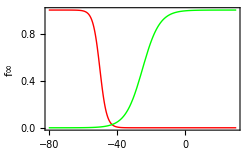

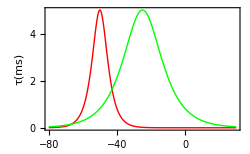

```mathematica
f[V_,V0_,S0_]:=0.5(1+Tanh[(V-V0)/(2S0)]);
τ[V_,V0_,S0_,ϕ_]:=ϕ/Cosh[(V-V0)/(2S0)];
Plot[{f[V,-50,-2],f[V,-25,5]},{V,-80,30},PlotRange->All,AxesOrigin->{-80,0},Frame->True,PlotStyle->{Red,Green},FrameLabel->{"V(mV)","f∞"},RotateLabel->False,ImageSize->250]
Plot[{τ[V,-50,-2,5],τ[V,-25,5,5]},{V,-80,30},PlotRange->All,AxesOrigin->{-80,0},Frame->True,PlotStyle->{Red,Green},FrameLabel->{"V(mV)","τ(ms)"},RotateLabel->False,ImageSize->250]
```

### Exercise 6: Using Cellerator™ to simulate simple enzyme networks

Use Cellerator™ to 
(i)  generate the equations for the ionic channel kinetics: S_1(⇌_k_3)^k_1 S_2→^k_2 S_3 in Exercise 1, solve these equations  (assuming k_1=2, k_2=2 and k_3=1 ) and plot graphs showing x, y ,z as a function of time starting from initial conditions of (a) x = 1, y = 0, z = 0; (b)  x = 0, y = 1, z = 0.  
(ii) generate the equations for allosteric enzyme kinetics in Exercise 7.

xlr8r 0.78 (20 Sept 2010) loaded 26 February 2012 at 12:43 GMT+00:59 using Mathematica 8.0 for Linux x86 (64-bit) (October 10, 2011) (Version 8., Release 4) (MathSBML 2.9.0 [8-Oct-2008])
GNU Lesser General Public License (LGPL) Terms Apply.

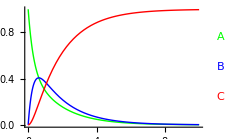

{{A→InterpolatingFunction[{{0.,10.}},<>],B→InterpolatingFunction[{{0.,10.}},<>],C→InterpolatingFunction[{{0.,10.}},<>]}}

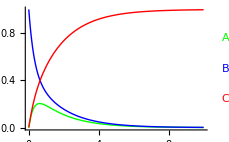

{{A→InterpolatingFunction[{{0.,10.}},<>],B→InterpolatingFunction[{{0.,10.}},<>],C→InterpolatingFunction[{{0.,10.}},<>]}}

```mathematica
<<xlr8r.m;
ionicChannel={
{A⇄B,2,1},{B->C,1}
};
r1=Quiet[run[interpret[ionicChannel],initialConditions-> {A[0]==1,B[0]==0,C[0]==0}, timeSpan->{0,10},plot->True
]]
r2=Quiet[run[interpret[ionicChannel],initialConditions-> {A[0]==0,B[0]==1,C[0]==0}, timeSpan->{0,10},plot->True
]]
```

```mathematica
allosteric={
{S+En ⇄C1,k1,km1},{C1 -> En+P,k2},
{S+C1 ⇄C2,k3,km3},{C2 -> C1+P,k4}
};
interpret[allosteric]
```

{{C1'[t]==-k2 C1[t]-km1 C1[t]+k4 C2[t]+km3 C2[t]-k3 C1[t] S[t]+k1 En[t] S[t],C2'[t]==-k4 C2[t]-km3 C2[t]+k3 C1[t] S[t],En'[t]==k2 C1[t]+km1 C1[t]-k1 En[t] S[t],P'[t]==k2 C1[t]+k4 C2[t],S'[t]==km1 C1[t]+km3 C2[t]-k3 C1[t] S[t]-k1 En[t] S[t]},{C1,C2,En,P,S}}

### Exercise 7: Allosteric enzyme kinetics (optional)

An allosteric enzyme E reacts with a substrate S to produce a product P according to the mechanism
      S + E (⇌_(k_-1))^k_1 C_1 →^k_2 E + P
      S + C_1 (⇌_(k_-3))^k_3 C_2→^k_4 C_1 + P
where the k's are rate constants and C_1 and C_2 enzyme-substrate complexes. With lower case letters denoting concentrations, and initial conditions s(0)=s_0, e(0)=e_0, c_1(0)=c_2(0)=p(0)=0 write down the differential equation model based on the Law of Mass Action. If  ϵ=e_0/s_0≪1, τ=k_1 e_0 t, u=s/s_0, v_i=c_i/e_0,  show that the nondimensional reaction mechanism reduces to 

     du/dτ=f(u,v_1,v_2),   dv_i/dτ=g_i(u,v_1,v_2),  i=1,2.

Determine f, g_1, g_2 and hence show that for τ≫ ϵ the uptake of u is governed by 
     
     du/dτ=-r(u)=-u(A+Bu)/(C+u+Du^2),
     
where A,B,C and D are positive parameters.  When k_2=0,  sketch the uptake rate r(u) as a function of u and compare it with the Michaelis-Menten uptake.

Assumptions to be made from law of mass action (write allosteric reaction in system of ODE's first):
e_0 = e(t) + c_1(t) + c_2(t)

Steps:
Reduce ds/dt in terms of u,v1,v2
For second part: dv1/dtau = 0, dv2/dtau = 0